## Patterns

### the Mathematica pattern matcher

Define a value for a symbol:

```mathematica
Clear[a]
```

```mathematica
a=1
```

1

Mathematica now contains a pattern for the symbol:

```mathematica
Information[a]
```

Global`a

a=1

```mathematica
?a
```

Global`a

a=1

... which it uses when the symbol is evaluated:

```mathematica
a
```

1

The evaluator applies the pattern until it gets an answer:

```mathematica
Trace[a+1]
```

{{a,1},1+1,2}

### Symbol definitions

Define a function:

```mathematica
f[x_]:=x+1
```

```mathematica
?f
```

Global`f

f[x_]:=x+1

... and a rule for a specific case:

```mathematica
f[2]=5
```

5

To evaluate f[1], the pattern matcher uses the first definition for f:

```mathematica
f[1]
```

2

But when the more specific rule applies, it takes precidence:

```mathematica
f[2]
```

5

Otherwise, the more general pattern is used:

```mathematica
f[1]===1+1
```

True

```mathematica
f[3]===3+1
```

True

Mathematica orders the definitions for f in order of more specific to more general:

```mathematica
?f
```

Global`f

f[2]=5
 
f[x_]:=x+1

```mathematica
DownValues[f]
```

{HoldPattern[f[2]]:>5,HoldPattern[f[x_]]:>x+1}

```mathematica
Clear[f]
```

```mathematica
f[2,y_]:=3
```

```mathematica
f[x_,3]:=2
```

```mathematica
f[2,3]
```

3

```mathematica
DownValues[f]
```

{HoldPattern[f[2,y_]]:>3,HoldPattern[f[x_,3]]:>2}

So more specific rules get applied first.

```mathematica
Clear[a]
```

```mathematica
x=2
```

2

```mathematica
a^2/.{x_:>x+1,y_^2:>y}
```

1+a^2

```mathematica
Clear[f]
```

```mathematica
f[2]=5
```

5

```mathematica
f[x_]:=x+1
```

```mathematica
DownValues[f]
```

{HoldPattern[f[2]]:>5,HoldPattern[f[x_]]:>x+1}

```mathematica
x=2
```

2

```mathematica
OwnValues[x]
```

{HoldPattern[x]:>2}

```mathematica
f[x]
```

```mathematica
f[2]
```

5

```mathematica
Clear[f]
```

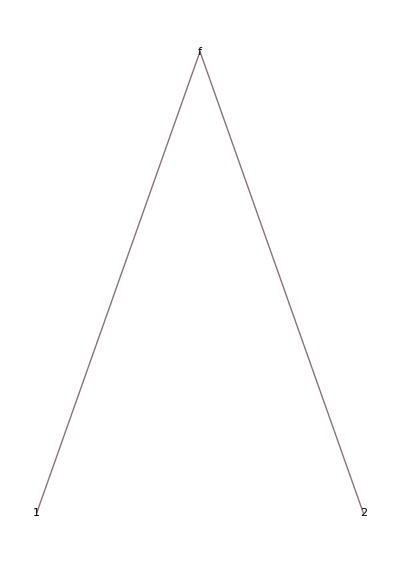

```mathematica
TreeForm[f[1,2]]
```

### Blank: _

To define a function, we used the pattern

```mathematica
x_
```

x_

Let’s use FullForm to get the full Mathematica expression for x_:

```mathematica
FullForm[x_]
```

Pattern[x,Blank[]]

Blank stands for any expression in a pattern.
So here, the function g can be called with any input:

```mathematica
g[x_]:=x+100
```

```mathematica
g[1]
```

101

```mathematica
g["a"]
```

100+a

```mathematica
g[{1,"a"}]
```

{101,100+a}

You can specify what the Head of the expression must be.
So here, the function h can only be called with an Integer:

```mathematica
h[y_Integer]:=y
```

```mathematica
h[s_String]:=Print["error!"]
```

So giving a String argument won't evaluate:

```mathematica
h["a"]
```

error!

```mathematica
Head["a"]
```

String

But given an Integer it will:

```mathematica
h[10]
```

10

```mathematica
Head[10]
```

Integer

## Cases

Cases is a function that returns the expressions in a list that match a pattern:

```mathematica
Clear[a]
```

```mathematica
Cases[{a,b,c},a]
```

{a}

```mathematica
Cases[{a,b,c,a},a]
```

{a,a}

You can specify what to return when there's a match:

```mathematica
Cases[{a,b,c,a},a->"match!"]
```

{match!,match!}

```mathematica
Cases[{a,b,c,a},a]
```

{a,a}

```mathematica
Select[{a,b,c,a},MatchQ[#,a]&]
```

{a,a}

```mathematica
Position[{a,b,c,a},a->1]
```

{}

Define a list of expressions:

```mathematica
alist={1,a,{a,a},a^a,2^a,Log[a],Hold[2^3],2^3}
```

{1,a,{a,a},a^a,2^a,Log[a],Hold[2^3],8}

Blank matches anything in the list:

```mathematica
Cases[alist,_]
```

{1,a,{a,a},a^a,2^a,Log[a],Hold[2^3]}

Specify the form of the expression to match:

```mathematica
Cases[alist,_^_]
```

{a^a,2^a}

```mathematica
Cases[alist,Log[_]]
```

{Log[a]}

```mathematica
Cases[alist,{_,_}]
```

{{a,a}}

```mathematica
Cases[alist,e_Symbol^_]
```

{a^a}

```mathematica
Cases[alist,_^e_->e]
```

{a,a}

```mathematica
ReleaseHold@Cases[alist,Hold[_^_]]
```

{8}

What if you want to match a Rule?

```mathematica
alist={1,a,{a,a},a^a,2^a,Log[a],Hold[2^3],d->dp,HoldPattern[d->da]}
```

{1,a,{a,a},a^a,2^a,Log[a],Hold[2^3],d→dp,HoldPattern[d→da]}

This won't work:

```mathematica
Cases[alist,d->dp]
```

{}

Use HoldPattern:

```mathematica
Cases[alist,(d->dp):>(d->dp)]
```

{d→dp}

```mathematica
FullForm[d->dp]
```

Rule[d,dp]

```mathematica
Cases[alist,Hold[2^3]]
```

{Hold[2^3]}

```mathematica
?Literal
```

System`Literal

Attributes[Literal]={HoldAll,Protected}

```mathematica
Cases[alist,_HoldPattern]
```

{HoldPattern[d→da]}

```mathematica
Cases[alist,HoldPattern[d->da]]
```

{}

```mathematica
Cases[alist,HoldPattern[HoldPattern[d->dp]]]
```

{d→dp}

```mathematica
Cases[alist,Verbatim[HoldPattern[d->da]]]
```

{HoldPattern[d→da]}

```mathematica
?Verbatim
```

Verbatim[expr] represents expr in pattern matching, requiring that expr be matched exactly as it appears, with no substitutions for blanks or other transformations.

```mathematica
Cases[{_,1},Verbatim[_]]
```

{_}

```mathematica
Cases[alist,HoldPattern[d->dp]]
```

{}

```mathematica
FullForm[d->dp]
```

Rule[d,dp]

```mathematica
Cases[alist,HoldPattern[d->dp]]
```

{d→dp}

```mathematica
Cases[alist,Verbatim[d->dp]]
```

{d→dp}

```mathematica
Cases[alist,Verbatim[Rule[d,dp]]]
```

{d→dp}

Specify more than one pattern to match using Alternatives:

```mathematica
Cases[alist,_[_^_]|_^_]
```

{a^a,2^a,Hold[2^3]}

```mathematica
Cases[alist,Alternatives[_[_^_],_^_]]
```

{a^a,2^a,Hold[2^3]}

Not to be confused with Or which is a double pipe: ||

```mathematica
Cases[alist,_[_^_]||_^_]
```

{}

Cases can take a level spec:

```mathematica
Cases[{a,b,c,a},a]
```

{a,a}

```mathematica
Cases[{a,b,c,a},a,1]
```

{a,a}

```mathematica
Cases[{{a,b,c,a}},a,1]
```

{}

```mathematica
Cases[{{a,b,c,a}},a,2]
```

{a,a}

The fourth argument specifies how many matches to return:

```mathematica
Cases[{{a,b,c,a}},a,2,1]
```

{a}

```mathematica
Cases[Exp[a+b],a+b]
```

{a+b}

```mathematica
FullForm[{a+b}]
```

List[Plus[a,b]]

```mathematica
?Cases
```

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern->rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern->rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern.

```mathematica
Options[Cases]
```

{Heads→False}

```mathematica
Cases[{Exp[a+b]},Exp[_]]
```

{ⅇ^(a+b)}

```mathematica
Cases[Exp[a+b],Exp[_],{0}]
```

{ⅇ^(a+b)}

```mathematica
Cases[Exp[a+b],Exp[_],{1,0}]
```

{}

```mathematica
Cases[Exp[a+b],Exp[_],{0,1}]
```

{ⅇ^(a+b)}

### BlankSequence: __

```mathematica
Clear[h]
```

Use __ to match one or more expressions:

```mathematica
h[x__]:={x}
```

```mathematica
h[1]
```

{1}

```mathematica
h[1,2]
```

{1,2}

```mathematica
h["first","second","third"]
```

{first,second,third}

Note that __ won't match zero expressions:

```mathematica
h[]
```

h[]

```mathematica
Clear[g]
```

### BlankNullSequence: __

Use BlankNullSequence, or ___, to match zero things:

```mathematica
f[x_,y_]:=x+y
```

```mathematica
f[Sequence@@{1,2}]
```

3

```mathematica
f@@{1,2}
```

3

```mathematica
List[Sequence[1,2],Sequence[2,3]]
```

{1,2,2,3}

```mathematica
f[Sequence@@{{1,2},{2,3}}]
```

{3,5}

```mathematica
g[x___]:=x
```

```mathematica
g[1,2,3]
```

Sequence[1,2,3]

```mathematica
g[1,2,{3}]
```

Sequence[1,2,{3}]

```mathematica
g[1,{3}]
```

Sequence[1,{3}]

```mathematica
g[]
```

Sequence[]

## Select vs Cases

```mathematica
Do[Select[{1,2,3,4},#==2&],{1000}];//AbsoluteTiming
```

{0.0033,Null}

```mathematica
Do[Cases[{1,2,3,4},2],{1000}];//AbsoluteTiming
```

{0.00218,Null}

## Application: find periodicity in a CA evolution

Let's use the patterns we've been talking about to try to find repetition in a CA evolution.

We expect there will be:
1. an initial transient
2. at some point the CA will produce a list that has occured before (marking one full cycle)
3. the cycle will continue forever (since the CA is deterministic)

So our pattern is: {transient, single list, cycle, single list again, repeating stuff}:

```mathematica
{t___,a_,m___,a_,___}
```

```mathematica
ca30=CellularAutomaton[30,{1,0,1,1,1},10]
```

{{1,0,1,1,1},{0,0,1,0,0},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0}}

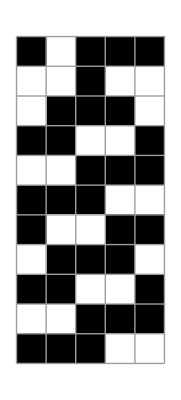

```mathematica
ArrayPlot[ca30,Mesh->True]
```

```mathematica
CellularAutomaton[30,{1,0,1,1,1},40]
```

{{1,0,1,1,1},{0,0,1,0,0},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0}}

```mathematica
e=CellularAutomaton[30,{1,0,1,1,1},40];
```

```mathematica
Cases[{e},{t___,Longest[a__],m___,Longest[a__],___}:>{{t},{a},{m}}]
```

{{{{1,0,1,1,1},{0,0,1,0,0}},{{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1},{0,1,1,1,0},{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0}},{{1,0,0,1,1}}}}

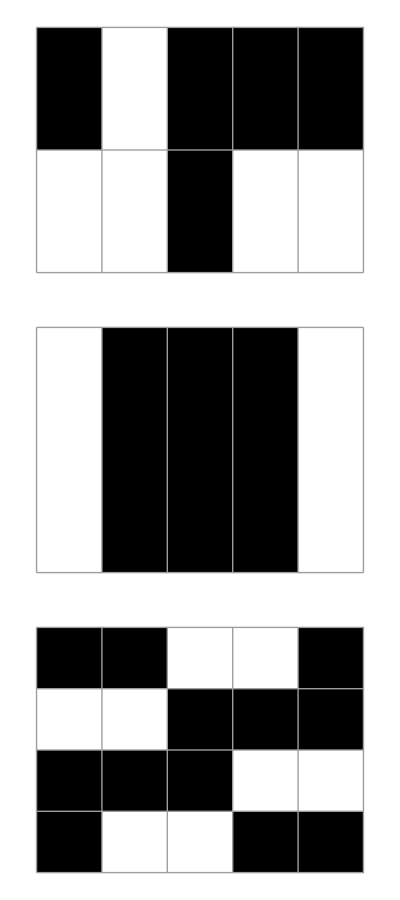
-Graphics--Graphics-

```mathematica
Row[{ArrayPlot[#,Mesh->True]&/@First@Cases[{e},{t___,a__,m___,a__,___}:>{{t},{a},{m}}]//Column,ArrayPlot[ca30,Mesh->True,ImageSize->100]}]
```

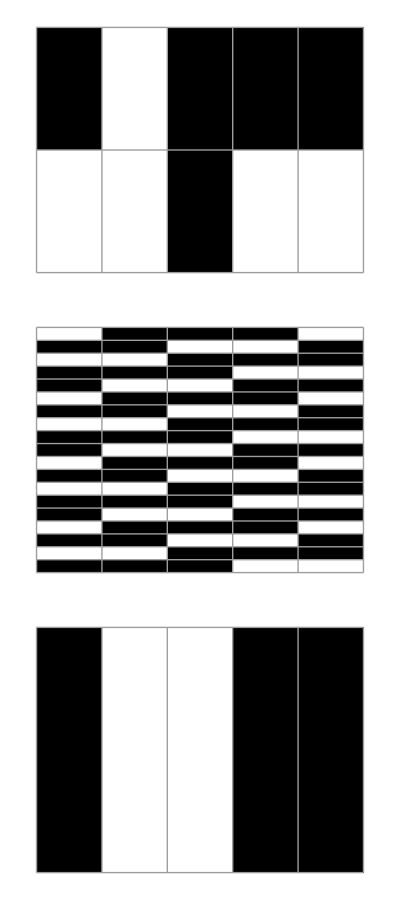
-Graphics--Graphics-

```mathematica
Row[{ArrayPlot[#,Mesh->True]&/@First@Cases[{e},{t___,Longest[a__],m___,Longest[a__],___}:>{{t},{a},{m}}]//Column,ArrayPlot[e,Mesh->True,ImageSize->100]}]
```

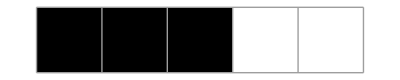
-Graphics-
-Graphics--Graphics-

```mathematica
Row[{ArrayPlot[#,Mesh->True]&/@First@Cases[{e},{t___,Shortest[a__]..}:>{{t},{a}}]//Column,ArrayPlot[e,Mesh->True,ImageSize->100]}]
```

```mathematica
Cases[{e2},{t___,a_,m___,a_,___}:>{{t},{a},{m}}];//AbsoluteTiming
```

{0.005794,Null}

```mathematica
Cases[{e3},{t___,a_,m___,a_,___}:>{{t},{a},{m}}];//AbsoluteTiming
```

{0.36874,Null}

```mathematica
N@Log[2,4000]
```

11.9658

```mathematica
times=Table[{2^n,First@AbsoluteTiming[Cases[{e3[[1;;2^n]]},{t___,a_,m___,a_,___}:>{{t},{a},{m}}]]},{n,1,10,1}]
```

{{2,0.000082},{4,0.000049},{8,0.000078},{16,0.000095},{32,0.00016},{64,0.00033},{128,0.000817},{256,0.00247},{512,0.008752},{1024,0.02812}}

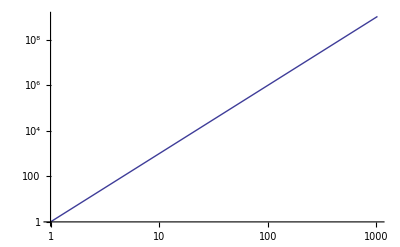

```mathematica
LogLogPlot[n^3,{n,1,1024}]
```

```mathematica
N@Log[times[[4;;10]]]
```

{{2.77259,-9.26163},{3.46574,-8.71564},{4.15888,-8.02555},{4.85203,-7.10987},{5.54518,-6.00394},{6.23832,-4.73847},{6.93147,-3.57138}}

```mathematica
{fa,fb}={a,b}/.FindFit[N@Log[times[[4;;10]]],a*x+b,{a,b},x]
```

{1.39358,-13.5369}

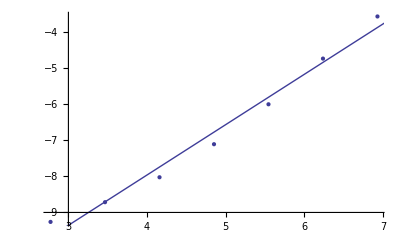

```mathematica
Show[{ListPlot[N@Log[times[[4;;10]]],Mesh->All],Plot[fa*x+fb,{x,1,1024}]}]
```

```mathematica
x^3/2
```

```mathematica
Cases[{CellularAutomaton[30,{1,0,1,1,1},40]},{t___,a_,m___,a_,___}:>{{t},{a},{m}}]
```

```mathematica
Cases[CellularAutomaton[30,{1,0,1,1,1},40],{t___,a_,m___,a_,___}->{{a},{m}},{0}]
```

{{{1},{{1,1,0,0,1},{0,0,1,1,1},{1,1,1,0,0},{1,0,0,1,1}}}}

```mathematica
ArrayPlot[#,Mesh->True]&/@
Flatten[Cases[{CellularAutomaton[30,{1,0,1,1,1},40]},{t___,a_,m___,a_,___}:>{{t},{a},{m}}],
1
]//Column
```

-Graphics-

Some subtle points about the pattern I glossed over:

```mathematica
{t___,a_,m___,a_,___}
```

1. Note we used BlankNullSequence (triple underscore: ___) for the transient t___ and the middle stuff m___, since these could in fact be of zero length (i.e. there may be no transient, and/or the single list a_ could be repeating with nothing in between).
2. We also needed to match zero or more rows at the end, since the evolution might happen to stop exactly after one cycle.

Note also that this isn't the fastest way to check for repeating patterns in a CA evolution.  One alternative would be to use

## Application: removing the background of a CA

Here's one row in a CA evolution:

```mathematica
l={1,1,1,1,1,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1}
```

{1,1,1,1,1,1,1,1,1,0,1,0,1,0,1,1,1,1,1,1,1,1,1}

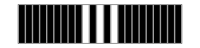

```mathematica
ArrayPlot[{l},Mesh->True,ImageSize->200]
```

We want to remove the background, so that the stuff out to the sides is white (zero).
So we want to subtract the value on the background.
Define the background color as the max value of the two ends of the row:

```mathematica
Max[First@l,Last@l]
```

1

Subtract the background from the row:

```mathematica
l-Max[First@l,Last@l]
```

{0,0,0,0,0,0,0,0,0,-1,0,-1,0,-1,0,0,0,0,0,0,0,0,0}

... and take the result Mod 2, to make sure the colors are still in the range [0,1]:

```mathematica
Mod[l-Max[First@l,Last@l],2]
```

{0,0,0,0,0,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0}

Here's the result:

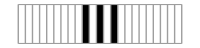

```mathematica
ArrayPlot[{Mod[l-Max[First@l,Last@l],2]},Mesh->True,ImageSize->200]
```

Define a function that does this for the entire CA evolution:

```mathematica
Clear@Clean
```

```mathematica
Clean[ca_,k_:2]:=Drop[Mod[#-Max[First[#],Last[#]],k]&/@ca,-1]
```

```mathematica
CellularAutomaton[{8111,2,3/2},{{1},0},{10,All}]
```

{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0}}

```mathematica
ArrayPlot[CellularAutomaton[{8111,2,3/2},{{1},0},{10,All}]]
```

-Graphics-

```mathematica
ArrayPlot[Clean@CellularAutomaton[{8111,2,3/2},{{1},0},{10,All}]]
```

-Graphics-

```mathematica
ArrayPlot[CellularAutomaton[{7178690,{3,{3,1,3}}},{{1},0},{100,All}],PixelConstrained->1]
```

-Graphics-

```mathematica
ArrayPlot[Clean[CellularAutomaton[{7178690,{3,{3,1,3}}},{{1},0},{100,All}],3],PixelConstrained->1]
```

-Graphics-

```mathematica
randomrules=RandomInteger[{0,2^(2^4)},10];
```

```mathematica
Column[With[{e=CellularAutomaton[{#,2,3/2},{{1},0},{10,All}]},Grid[{{ArrayPlot@e,ArrayPlot@Clean@e}}]]&/@randomrules]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

## Application: detect boundaries in a CA

Now that we've removed the background, it's easier to see the most interesting part of the evolution.

```mathematica
simpleca=CellularAutomaton[{8111,2,3/2},{{1},0},{10,All}];
```

```mathematica
ArrayPlot[simpleca]
```

-Graphics-

```mathematica
ArrayPlot[Clean@simpleca]
```

-Graphics-

Now we want to detect the boundaries of the interesting behavior.

The basic idea is to use Differences to find the part of the evolution that differs from the background.
Differences takes the difference between successive pairs in the list:

```mathematica
Differences[{a,b,c,d}]
```

{-a+b,-b+c,-c+d}

Here's a different way of doing the same thing:

```mathematica
#[[2]]-#[[1]]&/@Partition[{a,b,c,d},2,1]
```

{-a+b,-b+c,-c+d}

Take a row in the evolution after the background has been removed:

```mathematica
Clean[simpleca][[9]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0}

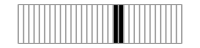

```mathematica
ArrayPlot[{Clean[simpleca][[9]]},Mesh->True,ImageSize->200]
```

Differences gives the parts that differ from the background:

```mathematica
Differences[Clean[simpleca][[9]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0}

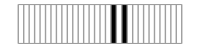

```mathematica
ArrayPlot[{Differences[Clean[simpleca][[9]]]},Mesh->True,ImageSize->200]
```

We're really just interested in the positions where the pattern differs from the background:

```mathematica
Differences[Clean[simpleca][[9]]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,-1,0,0,0,0,0,0,0,0,0,0}

```mathematica
Position[Differences[Clean[simpleca][[9]]],x_/;x!=0,{1}]
```

{{18},{20}}

```mathematica
Position[#,x_/;x!=0]&/@Map[Differences,Clean@simpleca]//Column
```

{{10},{11}}
{{11},{12}}
{{12},{14}}
{{13},{14}}
{{14},{16}}
{{15},{16}}
{{16},{18}}
{{17},{18}}
{{18},{20}}
{{19},{20}}

```mathematica
Boundaries[ca_]:=Module[{a},Flatten[If[(a=Position[#,x_/;x!=0])=={},{},Union@{a[[1]]+1,a[[-1]]}]]&/@Map[Differences,ca]]
```

```mathematica
Boundaries[simpleca]
```

{{11},{12},{13,14},{14},{15,16},{16},{17,18},{18},{19,20},{20},{21,22}}

```mathematica
ArrayPlot[Clean@simpleca,Mesh->True]
```

-Graphics-

Left boundary

```mathematica
First/@Boundaries[simpleca]
```

{11,12,13,14,15,16,17,18,19,20,21}

Right boundary

```mathematica
Last/@Boundaries[simpleca]
```

{11,12,14,14,16,16,18,18,20,20,22}

## references

** Inspired by a posting on the NKS forum by Jesse Nochella: 
Jesse Nochella, “period[{a___, x_, b___, x_, c___}] := {Length@{x, b, x}, {x, b, x}, Length@{a}}”, posting on forum.wolframscience, May 24, 2005.